# Case Versus Phylogentic Likelihood

```mathematica
col1 = ColorData[97][1]
```

RGBColor[0.368417, 0.506779, 0.709798]

```mathematica
col2 = ColorData[97][2]
```

RGBColor[0.880722, 0.611041, 0.142051]

## Global Events

Simulating a tree

```mathematica
increment[Δt_,sVecIn_,treeMtrxIn_]:=Block[{j,sVec,treeMtrx},
{sVec,treeMtrx}={sVecIn,treeMtrxIn};
For[j=1,j≤Length[treeMtrx],j++,
If[sVec[[j]]>0,treeMtrx[[j,j]]+=Δt]
];
{sVec,treeMtrx}
]
```

```mathematica
(*Birth*)
birth[Δt_,sVecIn_,treeMtrxIn_]:=Block[{n,sVec,treeMtrx,temp},
{sVec,treeMtrx}=increment[Δt,sVecIn,treeMtrxIn];
n=RandomChoice[Flatten[Position[sVec,_?(#>0&)]]];
(*Add element to sVec*)
AppendTo[sVec,1];
(*Add row to treeMtrx*)
AppendTo[treeMtrx,treeMtrx[[n]]];
temp=Transpose[treeMtrx];
treeMtrx=Transpose[AppendTo[temp,Join[treeMtrx[[n]],{t}]]];
{sVec,treeMtrx}
]
```

```mathematica
death[Δt_,sVecIn_,treeMtrxIn_]:=Block[{n,sVec,treeMtrx,temp},
{sVec,treeMtrx}=increment[Δt,sVecIn,treeMtrxIn];
n=RandomChoice[Flatten[Position[sVec,_?(#>0&)]]];
(*Change state of lin*)
sVec[[n]]=0;
{sVec,treeMtrx}
]
```

```mathematica
samplingWReplacement[Δt_,sVecIn_,treeMtrxIn_]:=Block[{n,sVec,treeMtrx,temp},
{sVec,treeMtrx}=increment[Δt,sVecIn,treeMtrxIn];
n=RandomChoice[Flatten[Position[sVec,_?(#>0&)]]];
(*Add element to sVec*)
AppendTo[sVec,-1];
(*Add row to treeMtrx*)
AppendTo[treeMtrx,treeMtrx[[n]]];
temp=Transpose[treeMtrx];
treeMtrx=Transpose[AppendTo[temp,Join[treeMtrx[[n]],{t}]]];
{sVec,treeMtrx}
]
```

```mathematica
samplingWOutReplacement[Δt_,sVecIn_,treeMtrxIn_]:=Block[{n,sVec,treeMtrx,temp},
{sVec,treeMtrx}=increment[Δt,sVecIn,treeMtrxIn];
n=RandomChoice[Flatten[Position[sVec,_?(#>0&)]]];
(*Change state of lin*)
sVec[[n]]=-1;
{sVec,treeMtrx}
]
```

```mathematica
samplingρ[Δt_,ρ_,sVecIn_,treeMtrxIn_]:=Block[{nList,sVec,treeMtrx,temp},
{sVec,treeMtrx}={sVecIn,treeMtrxIn};
nList=Flatten[Position[sVec,_?(#>0&)]];
Do[
treeMtrx[[n,n]]+=Δt;
If[RandomReal[]<ρ,sVec[[n]]=-1,sVec[[n]]=0];
,{n,nList}];
{sVec,treeMtrx}
]
```

```mathematica
nearNeighbour[treeMtrx_]:=Block[{UTM,pos},
UTM=UpperTriangularize[treeMtrx,1];
Position[UTM,Max[UTM]][[1]]//Sort
]
```

```mathematica
newick[treeMtrx_]:=Block[{treeTenp,order,l1,l2},
(*Initialize*)
order=Table[x,{x,1,Length[treeMtrx]}];
treeTenp=treeMtrx;
While[Length[treeTenp]>1,
{l1,l2}=nearNeighbour[treeTenp];
(*Update trMtrx and sMtrx*)
Print[{treeTenp[[l1,l1]]-treeTenp[[l1,l2]],treeTenp[[l2,l2]]-treeTenp[[l1,l2]]}];
treeTenp[[l1,l1]]=treeTenp[[l1,l2]];
treeTenp=Delete[treeTenp,l2];
treeTenp=Transpose[Delete[Transpose[treeTenp],l2]];
order[[l1]]=order[[{l1,l2}]];
order=Delete[order,l2];
];
order
];
```

```mathematica
newickText[treeMtrx_]:=Block[{treeTenp,order,l1,l2},
(*Initialize*)
order=Table[ToString[x],{x,1,Length[treeMtrx]}];
treeTenp=treeMtrx;
While[Length[treeTenp]>1,
{l1,l2}=nearNeighbour[treeTenp];
(*Update trMtrx and sMtrx*)
order[[l1]]={"{"<>order[[l1]]<>"}:"<>ToString[treeTenp[[l1,l1]]-treeTenp[[l1,l2]]]<>","<>"{"<>order[[l2]]<>"}:"<>ToString[treeTenp[[l2,l2]]-treeTenp[[l1,l2]]]};
treeTenp[[l1,l1]]=treeTenp[[l1,l2]];
treeTenp=Delete[treeTenp,l2];
treeTenp=Transpose[Delete[Transpose[treeTenp],l2]];
order=Delete[order,l2];
];
order=ToString[order];
order=StringReplace[order,{"{"->"(","}"->")"}];
order=StringReplace[order,Table["("<>ToString[j]<>")"->ToString[j],{j,1,Length[treeMtrx]}]];
order
];
```

```mathematica
sampCt[treeMtrx_,Τ_]:=Block[{treeTenp,fTips,eTips,fAns,,l1,l2},
fTips=0;eTips=0;fAns=0;
eTips=Length[Select[Diagonal[treeMtrx],#==Τ&]];
fTips=Length[treeMtrx]-eTips;
treeTenp=treeMtrx;
While[Length[treeTenp]>1,
{l1,l2}=nearNeighbour[treeTenp];
If[treeTenp[[l2,l2]]-treeTenp[[l1,l2]]==0,fAns++;fTips--];
If[treeTenp[[l1,l1]]-treeTenp[[l1,l2]]==0,fAns++;fTips--];
(*Update trMtrx and sMtrx*)
treeTenp[[l1,l1]]=treeTenp[[l1,l2]];
treeTenp=Delete[treeTenp,l2];
treeTenp=Transpose[Delete[Transpose[treeTenp],l2]];
];
{eTips,fTips,fAns}
]
```

## Simulating SIR Trees

```mathematica
testParsSIR={β->1,κ->100,γ->0.2,ψ->0.4,r->1,ρ->0,Τ->20};
```

```mathematica
Clear[testParsSIR2]
testParsSIR2[intS_]:=testParsSIR2[intS]={β->RandomReal[{0.2,3}],κ->100,γ->0.2,ψ->0.4,r->1,ρ->0,Τ->20};
```

State Vector {t, S, I, R,I*}

```mathematica
ratesSIR[Se_]:={(*transmission*)(β Se[[2]]Se[[3]])/κ,(*recover*)γ Se[[3]],(*sampling w/out removal*)ψ (1-r) Se[[3]],(*samp w removal*)ψ r Se[[3]]};
```

```mathematica
ΔSeSIR[Δt_]:={{Δt,-1,1,0,0},{Δt,0,-1,1,0},{Δt,0,0,0,1},{Δt,0,-1,1,1}}
```

```mathematica
ΔDivSIR[Δt_,e_,sVecIn_,treeMtrxIn_]:=Block[{sVec,treeMtrx},
If[e==1, {sVec,treeMtrx}=birth[Δt,sVecIn,treeMtrxIn],
If[e==2, {sVec,treeMtrx}=death[Δt,sVecIn,treeMtrxIn],
If[e==3, {sVec,treeMtrx}=samplingWReplacement[Δt,sVecIn,treeMtrxIn],
If[e==4, {sVec,treeMtrx}=samplingWOutReplacement[Δt,sVecIn,treeMtrxIn],Print["Error"]]]]];
{sVec,treeMtrx}
]
```

```mathematica
Clear[simSIR,simSIREpi]
simSIR[pars_,intS_]:=simSIR[pars,intS]=Block[{sVec,treeMtrx,Se,t,temp, Δt,e,x},
(*Initialize*)
t=0; Se={{0,κ-1,1,0,0}}/.pars;
sVec={1};treeMtrx={{0}};
(*Firt event*)
temp=ratesSIR[Se[[-1]]]/.pars;
Δt=RandomVariate[ExponentialDistribution[Total[temp]]];
(*For[x=1,x<=2,x++,*)
While[t+Δt<(Τ/.pars),
t=t+Δt;
(*Choose Event*)
e=RandomChoice[temp->{1,2,3,4}];
(*Update State*)
Se=AppendTo[Se,Se[[-1]]+ΔSeSIR[Δt][[e]]];
{sVec,treeMtrx}=ΔDivSIR[Δt,e,sVec,treeMtrx];
(*Choose Next Δt*)
temp=ratesSIR[Se[[-1]]]/.pars;
If[Total[temp]>0,
Δt=RandomVariate[ExponentialDistribution[Total[temp]]],Δt=Τ/.pars];
];
simSIREpi[pars,intS]=Se;
(*Present-day Sampling*)
{sVec,treeMtrx}=samplingρ[Τ-t/.pars,ρ/.pars,sVec,treeMtrx];
{sVec,treeMtrx}
]
```

```mathematica
simSIR[testParsSIR,1];
```

This function is used for retrieving time which we can use it later for curve fitting

```mathematica
simSIREpi2[pars_,intS_]:=Block[{},
simSIR[pars,intS];
simSIREpi[pars,intS]
]
```

```mathematica
simSIREpi2[testParsSIR,2];
```

```mathematica
smpOut = 4
```

4

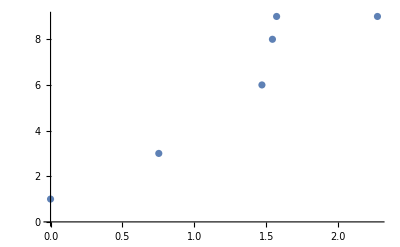

```mathematica
Transpose[{simSIREpi2[testParsSIR,smpOut][[;;,1]],Accumulate[simSIREpi2[testParsSIR,smpOut][[;;,3]]]}]//ListPlot
```

Creating the sampled tree.

```mathematica
(*List of Lineages in the sampled tree*)
sampTreeSIR[pars_,intS_]:=Block[{linList},
linList=Flatten[Position[simSIR[pars,intS][[1]],_?(#==-1&)]];
simSIR[pars,intS][[2]][[linList,linList]]]
```

```mathematica
yVec[pars_,intS_]:=(Τ/.pars)-Diagonal[sampTreeSIR[pars,intS]]
xVec[pars_,intS_]:=(Τ/.pars)-DeleteDuplicates[DeleteCases[Flatten[UpperTriangularize[sampTreeSIR[pars,intS],1]],0.]]
```

```mathematica
cVec[pars_,intS_]:=Diagonal[sampTreeSIR[pars,intS]]
```

```mathematica
yVec[testParsSIR,6]
```

{17.2474,17.1494,16.9049,18.1917,14.3861,16.7864,17.0981,16.6463,14.6858,15.677,12.0198,14.8719,11.2384,11.2849,13.2058,11.2273,11.8265,12.8659,11.9342,11.4033,11.5896,10.0106,10.6981,11.438,11.5317,10.5285,9.65902,10.3576,10.008,11.0694,10.5006,10.8512,9.67397,8.6169,6.25625,7.8129,8.82091,0.679787,7.06333,5.37722,5.21351,4.97181}

```mathematica
cVec[testParsSIR,6]
```

{2.75258,2.85061,3.09513,1.80828,5.61394,3.21358,2.90194,3.35369,5.31422,4.32301,7.98018,5.12808,8.76159,8.71514,6.79417,8.77272,8.17354,7.1341,8.0658,8.59672,8.41042,9.98942,9.30187,8.56203,8.46828,9.47148,10.341,9.64239,9.99204,8.9306,9.49937,9.14885,10.326,11.3831,13.7437,12.1871,11.1791,19.3202,12.9367,14.6228,14.7865,15.0282}

```mathematica
testTreeList=Flatten[Position[Table[Length[cVec[testParsSIR2[j],j]],{j,1,100}],_?(#>1&)]];
```

```mathematica
cVec[testParsSIR2[33],33]
```

{0.167119,1.9709,2.00784,1.37647,3.72742,2.85286,4.10435,4.05534,5.45594,3.23751,4.14671,6.32593,3.51766,4.07677,3.93798,4.67783,9.0731,6.14841,9.41574,7.655,9.41453,6.87484,6.94512,9.86277,7.61414,9.2592,9.88407,9.19829,9.5424,12.584,9.7952,8.6175,13.7101,10.234,12.1266,10.4244,10.8384,17.3687,11.6418,10.2778,10.122,10.8566,12.3061,9.67765,11.2761,11.3084,9.97314,12.0383,9.75227,11.2233,10.2126,14.3021,11.8876,11.822,12.3381,11.6298,11.429,13.7385,12.1701,11.7831,12.3509,15.3255,14.2762}

## Case Likelihood

```mathematica
sampTreeSIR[testParsSIR,testTreeList[[2]]]
```

{{1.20245,0.265082,0.837037,0.837037},{0.265082,1.69475,0.265082,0.265082},{0.837037,0.265082,2.08352,2.06944},{0.837037,0.265082,2.06944,2.35808}}

```mathematica
β/.testParsSIR2[testTreeList[[2]]]
```

2.56706

```mathematica
newickText[sampTreeSIR[testParsSIR,testTreeList[[2]]]]
```

(((1:0.365414,(3:0.0140812,4:0.288638):1.2324):0.571955,2:1.42967))

```mathematica
Export["/Users/siavashriazi/Desktop/SFU/iqtree-2.2.2.6-MacOSX/trees.nwk",%,"Text"]
```

/Users/siavashriazi/Desktop/SFU/iqtree-2.2.2.6-MacOSX/trees.nwk

## Numerical Integrate SIR

```mathematica
odes={D[x[t],t]==-β/κ x[t]y[t],D[y[t],t]==β/κ x[t]y[t]-(γ+ψ r) y[t],D[z[t],t]==(γ+ψ r)y[t]};
vars={x[t],y[t],z[t]};
inits={x[0]==κ-1,y[0]==1,z[0]==0};
Clear[nSIR]
nSIR[pars_]:=nSIR[pars]=NDSolve[Join[odes,inits]/.pars,vars,{t,0,Τ/.pars}][[1]]
nSsol[pars_,t2_]:=x[t]/.nSIR[pars]/.t->t2
nIsol[pars_,t2_]:=y[t]/.nSIR[pars]/.t->t2
nRsol[pars_,t2_]:=z[t]/.nSIR[pars]/.t->t2
```

```mathematica
nIsol[testParsSIR,20]
```

1.41661

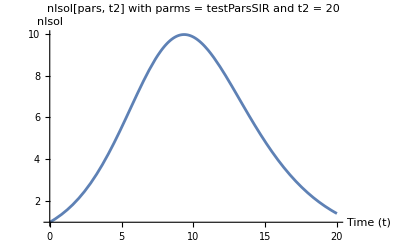

```mathematica
Plot[nIsol[testParsSIR,20],{t,0,20},PlotLabel->"nIsol[pars, t2] with parms = testParsSIR and t2 = 20",AxesLabel->{"Time (t)","nIsol"},PlotRange->All]
```

```mathematica
testParsSIR
```

{β→1,κ→100,γ→0.2,ψ→0.4,r→1,ρ→0,Τ→20}

```mathematica
Idata=Table[{t,nIsol[testParsSIR,t]},{t,0,20}]
```

{{0,1.},{1,1.46868},{2,2.12599},{3,3.0148},{4,4.15563},{5,5.51673},{6,6.98435},{7,8.35863},{8,9.39955},{9,9.91453},{10,9.83533},{11,9.2325},{12,8.26691},{13,7.12055},{14,5.94594},{15,4.84602},{16,3.87615},{17,3.05612},{18,2.38333},{19,1.84326},{20,1.41661}}

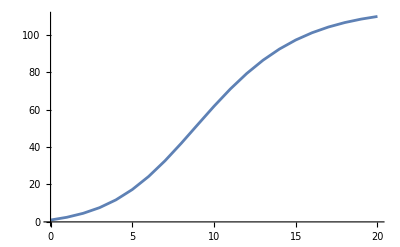

```mathematica
Iaccudata=Transpose[{Idata[[All,1]],Accumulate[Idata[[All,2]]]}]//ListLinePlot
```

## Calculate Likelihood

where

First, lets deal with the integral.

 
Note that

```mathematica
Clear[Ω]
Ω[pars_]:=Ω[pars]=Block[{tab,Δt},
Δt=Τ/100/.pars;
tab=Table[{Δt,Δt (ψ/.pars) nIsol[pars,t2]},{t2,0,Τ/.pars,Δt}];
tab=Join[{{0,0}},Accumulate[tab]];
Interpolation[tab]
]
```

Calculating the probability of observing a case:

```mathematica
PrC[j_,cVec_,pars_]:=(ψ /.pars)nIsol[pars,cVec[[j]]] Exp[-(Ω[pars][cVec[[j]]]-Ω[pars][If[j==1,0,cVec[[j-1]]]])]
```

Calculating the likelihood of observing a case:

```mathematica
ℒCase[cVec_,pars_]:=Product[PrC[j,cVec,pars],{j,1,Length[cVec]}]
```

#### Conditioning

Conditioning of the likelihood we need to multiply the likelihood by:

Where C(0) is probability of observing no case

```mathematica
𝒞[pars_]:=1-Exp[-Ω[pars][Τ/.pars]]
```

```mathematica
ℒCaseCond[cVec_,pars_]:=Product[PrC[j,cVec,pars],{j,1,Length[cVec]}]/𝒞[pars]
```

```mathematica
testTreeList
```

{2,3,4,5,6,7,8,12,13,15,16,17,18,19,22,23,32,33,38,39,40,42,46,47,49,50,51,52,53,54,55,56,58,60,61,62,64,66,67,70,72,73,74,75,78,79,80,81,83,84,85,87,88,89,90,91,92,94,95,96,98}

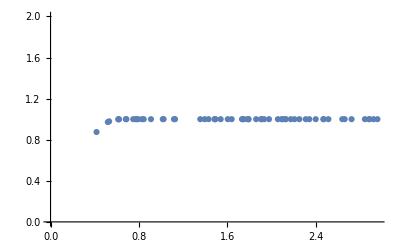

```mathematica
Table[{β/.testParsSIR2[intS],𝒞[testParsSIR2[intS]]},{intS,testTreeList}]//ListPlot
```

### Testing

Recall that the true parameters are...

```mathematica
likPars[βin_]=Join[{β->βin},testParsSIR[[2;;]]];
```

The likelihood surface

```mathematica
Clear[ℒCList]
ℒCList[intS_]:=ℒCList[intS]=Block[{cVecTest,out,Δβ,temp},
cVecTest=cVec[testParsSIR2[intS],intS];
Δβ=0.02;
If[Length[cVecTest]==0,out="No Tree",
out=Table[{β,ℒCaseCond[cVecTest,likPars[β]]},{β,0.8,3,Δβ}];
temp=Total[out[[;;,2]]Δβ];
out=Map[{#[[1]],(#[[2]])/temp}&,out];
];
out
]
```

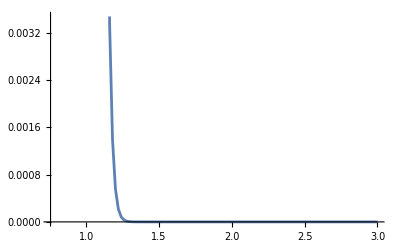

```mathematica
ListLinePlot[ℒCList[33]]
```

Calculating maximum posterior estimate of case likelihood

```mathematica
ℒCMPE[intS_]:=Block[{cVecTest,out,temp},
cVecTest=cVec[testParsSIR2[intS],intS];
If[Length[cVecTest]==0,out="No Tree",
out=Sort[ℒCList[intS],#1[[2]]>#2[[2]]&][[1,1]];
];
out
]
```

Calculating confidence interval of case likelihood

```mathematica
ℒCCI[intS_]:=Block[{cVecTest,out,temp,temp2,temp3,Δβ,ℒInt},
cVecTest=cVec[testParsSIR2[intS],intS];
If[Length[cVecTest]==0,out="No Tree",
(*Extract the Δβ step*)
Δβ=ℒCList[intS][[2,1]]-ℒCList[intS][[1,1]];
(*Convert Probilibty densities into probability by dividing the PDF into Δβ steps*)
temp=Map[{#[[1]],#[[2]]Δβ}&,ℒCList[intS]];
(*Sort the probabilities*)
temp=Sort[temp,#1[[2]]>#2[[2]]&];
(*Integrate the probabilites*)
temp2=Transpose[{temp[[;;,1]],Accumulate[temp[[;;,2]]]}];
(*β Values in the CI*)
temp3=Select[temp2,#[[2]]<0.95&][[;;,1]];
out=temp3
];
out
]
```

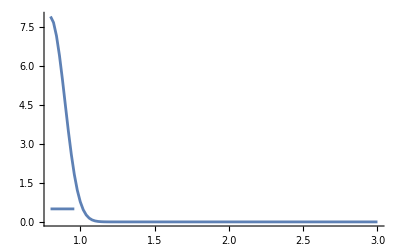

```mathematica
Show[ListLinePlot[ℒCList[33],PlotRange->All],ListLinePlot[Map[{#,0.5}&,ℒCCI[33]]],PlotRange->All]
```

## Phylogenetic Likelihood

```mathematica
λ[τ_,pars_]:=(β/κ/.pars)nSsol[pars,(Τ/.pars)-τ]
```

```mathematica
Clear[nEsol]
```

```mathematica
Clear[nsolE]
nsolE[pars_]:=nsolE[pars]=NDSolve[{D[e[τ],τ]==-(λ[τ,pars]+γ+ψ)e[τ]+λ[τ,pars] e[τ]^2+γ/.pars,e[0]==1},e[τ],{τ,0,Τ/.pars}][[1]]
nEsol[τ2_,pars_]:=e[τ]/.nsolE[pars]/.τ->τ2
```

```mathematica
Clear[ΦArg]
ΦArg[pars_]:=ΦArg[pars]=Block[{tab,Δt},
Δt=Τ/100/.pars;
tab=Table[{Δt,Δt (-((λ[t2,pars]+γ+ψ)/.pars)+2λ[t2,pars]nEsol[t2,pars])},{t2,0,Τ/.pars,Δt}];
tab=Join[{{0,0}},Accumulate[tab]];
Interpolation[tab]
]
```

```mathematica
Φ[τ_,pars_]:=Exp[ΦArg[pars][τ]]
```

Calculating likelihood of phylogeny:

```mathematica
ℒPhy[xVec_,yVec_,pars_]:=Block[{out,i,j},
out=Φ[Τ/.pars,pars];
For[i=1,i<=Length[xVec],i++,
out*=λ[xVec[[i]],pars]Φ[xVec[[i]],pars]
];
For[j=1,j<=Length[yVec],j++,
out*=(ψ/.pars)/Φ[yVec[[j]],pars]
];
out
]
```

## Conditioning on Phylogeny

To condition the likelihood we need to multiply by:

```mathematica
ℒPhyCond[xVec_,yVec_,pars_]:=Block[{out,i,j,denominator},out=Φ[Τ/. pars,pars];
For[i=1,i<=Length[xVec],i++,out*=λ[xVec[[i]],pars] Φ[xVec[[i]],pars]];
For[j=1,j<=Length[yVec],j++,out*=(ψ/. pars)/Φ[yVec[[j]],pars];];
denominator=1-nEsol[(Τ/. pars),pars];
out/denominator]
```

```mathematica
LogℒPhy[xVec_,yVec_,pars_]:=Block[{out,i,j},
out=ΦArg[pars][Τ/.pars];
For[i=1,i<=Length[xVec],i++,
out+=Log[λ[xVec[[i]],pars]]+ΦArg[pars][xVec[[i]]]
];
For[j=1,j<=Length[yVec],j++,
out+=Log[ψ/.pars]-ΦArg[pars][yVec[[j]]]
];
out
]
```

```mathematica
LogℒPhy2[intS_,pars_]:=LogℒPhy[xVec[testParsSIR2[intS],intS],yVec[testParsSIR2[intS],intS],pars]
```

```mathematica
LogℒPhyCond[xVec_,yVec_,pars_]:=Block[{out,i,j,denom},
out=ΦArg[pars][Τ/.pars];
For[i=1,i<=Length[xVec],i++,
out+=Log[λ[xVec[[i]],pars]]+ΦArg[pars][xVec[[i]]]
];
For[j=1,j<=Length[yVec],j++,
out+=Log[ψ/.pars]-ΦArg[pars][yVec[[j]]]
];
denom=Log[1-nEsol[(Τ/. pars),pars]];
out=out-denom
]
```

```mathematica
LogℒPhyCond2[intS_,pars_]:=LogℒPhyCond[xVec[testParsSIR2[intS],intS],yVec[testParsSIR2[intS],intS],pars]
```

Creating a list of phylogeny likelihood:

```mathematica
Clear[ℒPList]
ℒPList[intS_]:=ℒPList[intS]=Block[{xVecTest,yVecTest,out,Δβ,temp,min},
xVecTest=xVec[testParsSIR2[intS],intS];
yVecTest=yVec[testParsSIR2[intS],intS];
Δβ=0.02;
If[Length[yVecTest]==0,out="No Tree",
out=Table[{β,LogℒPhyCond[xVecTest,yVecTest,likPars[β]]},{β,0.8,3,Δβ}];
out=Transpose[{out[[;;,1]],out[[;;,2]]}];
min=out[[;;,2]]//Min;
out=Map[{#[[1]],#[[2]]-min}&,out];
temp=Total[out[[;;,2]]Δβ];
out=Map[{#[[1]],(#[[2]])/temp}&,out];
];
out
]
```

Calculating maximum posterior estimate of phylogeny likelihood:

```mathematica
ℒPMPE[intS_]:=Block[{yVecTest,out},
yVecTest=yVec[testParsSIR2[intS],intS];
If[Length[yVecTest]==0,out="No Tree",
out=Sort[ℒPList[intS],#1[[2]]>#2[[2]]&][[1,1]]];
out
]
```

```mathematica
ℒPMPE[1]
```

0.8

Calculating confidence interval of phylogeny likelihood:

```mathematica
ℒPCI[intS_]:=Block[{yVecTest,out,temp,temp2,temp3,Δβ,ℒInt},
yVecTest=yVec[testParsSIR2[intS],intS];
If[Length[yVecTest]==0,out="No Tree",
Δβ=ℒPList[intS][[2,1]]-ℒPList[intS][[1,1]];
temp=Map[{#[[1]],#[[2]]Δβ}&,ℒPList[intS]];
temp=Sort[temp,#1[[2]]>#2[[2]]&];
temp2=Transpose[{temp[[;;,1]],Accumulate[temp[[;;,2]]]}];
(*β Values in the CI*)
out=Select[temp2,#[[2]]<0.95&][[;;,1]];
];
out
]
```

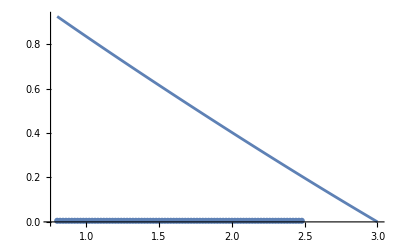

```mathematica
Show[ℒPList[1]//ListLinePlot,ListPlot[Map[{#,0.005}&,ℒPCI[1]]]]
```

## Comparing Case and Phylo

Calculating a likelihood surface for phylogeny and case counts given a tree

```mathematica
CompPlot[intS_]:=ListLinePlot[{ℒCList[intS],ℒPList[intS]},PlotRange->All]
```

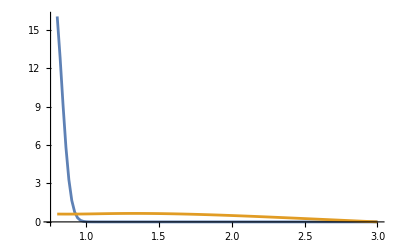

```mathematica
CompPlot[2]
```

```mathematica
CompPlot[intS_]:=Module[{betaValue},betaValue=β/. testParsSIR2[intS];
ListLinePlot[{ℒCList[intS],ℒPList[intS]},PlotRange->All,Epilog->{Red,Line[{{betaValue,0},{betaValue,5.5}}]}]]
```

```mathematica
testTreeList
```

{2,3,4,5,6,7,8,12,13,15,16,17,18,19,22,23,32,33,38,39,40,42,46,47,49,50,51,52,53,54,55,56,58,60,61,62,64,66,67,70,72,73,74,75,78,79,80,81,83,84,85,87,88,89,90,91,92,94,95,96,98}

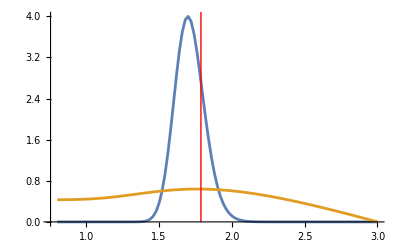

```mathematica
CompPlot[7]
```

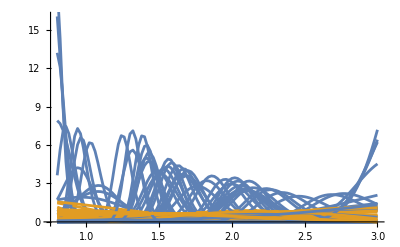

```mathematica
Show[Table[CompPlot[testTree],{testTree,testTreeList}]]
```

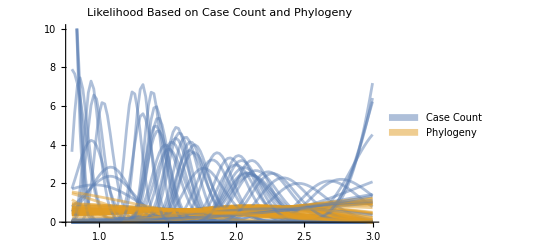

```mathematica
CompPlot[intS_List]:=Table[ListLinePlot[{ℒCList[testTree],ℒPList[testTree]},PlotRange->{Automatic,{0,10}},PlotStyle->{Directive[Opacity[0.5],col1],Directive[Opacity[0.5],col2]},PlotLabel->"Likelihood Based on Case Count and Phylogeny",FrameLabel->{"","Likelihood"}],{testTree,intS}];

legend=SwatchLegend[{Directive[Opacity[0.5],col1],Directive[Opacity[0.5],col2]},{"Case Count","Phylogeny"}];

Legended[Show[CompPlot[testTreeList]],Placed[legend,Right]]
```

plotting confidence interval and maximum posterior estimate for case counts and phylogeny likelihood per given tree

```mathematica
leg=PointLegend[{ColorData[97][1],ColorData[97][2],Red},{"Case","Phylo","Truth"}];
CICompPlot[intS_]:=Block[{βTrue},
βTrue=β/.testParsSIR2[intS];
Show[
(*Credible Intervals*)
ListLinePlot[{Map[{βTrue,#}&,ℒCCI[intS]],Map[{#,βTrue}&,ℒPCI[intS]]},AspectRatio->1,PlotStyle->{Directive[ColorData[97][1],Opacity[0.3]],Directive[ColorData[97][2],Opacity[0.3]]}],
(*Maximum Posterior Estimates*)
ListPlot[{{{βTrue,ℒCMPE[intS]}},{{ℒPMPE[intS],βTrue}},{{βTrue,βTrue}}},PlotMarkers->{Automatic, Medium},PlotStyle->{Automatic,Automatic,Red}],
PlotRange->{{0.8,3},{0.8,3}},Epilog->Inset[leg,Scaled[{0.9,0.12}]],Frame->True,Axes->False,FrameLabel->{" Phylogeny"," Case"},LabelStyle->Directive[Black, Medium]]]
```

```mathematica
Length[testTreeList]
```

61

maxn shows how many points do we want to show

```mathematica
maxn = 50
```

50

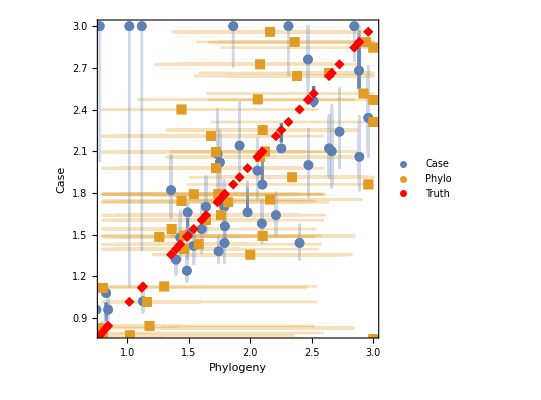

```mathematica
Show[Table[CICompPlot[testTreeList[[j]]],{j,1,maxn(*Length[testTreeList]*)}]]
```

```mathematica
(*Export["/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report/Figures/scatter.png",%]*)
```

```mathematica
testTreeList
```

{2,3,4,5,6,7,8,12,13,15,16,17,18,19,22,23,32,33,38,39,40,42,46,47,49,50,51,52,53,54,55,56,58,60,61,62,64,66,67,70,72,73,74,75,78,79,80,81,83,84,85,87,88,89,90,91,92,94,95,96,98}

```mathematica
observation = 1
```

1

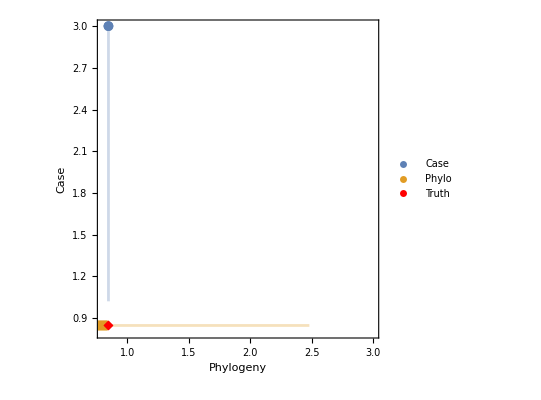

```mathematica
CICompPlot[observation]
```

plotting confidence interval and maximum posterior estimate for case counts and phylogeny likelihood per given tree

```mathematica
(*Clear[testParsSIR2]
testParsSIR2[intS_]:=testParsSIR2[intS]={β->RandomReal[{0.2,3}],κ->100,γ->0.2,ψ->0.4,r->1,ρ->0,Τ->20};*)
```

```mathematica
(*testTreeList=Flatten[Position[Table[Length[cVec[testParsSIR2[j],j]],{j,1,100}],_?(#>1&)]];*)
```

```mathematica
legCICase=PointLegend[{col1,Red},{"Case","Truth"}];
CICasePlot[intS_]:=Block[{βTrue},
βTrue=β/.testParsSIR2[intS];
Show[
(*Credible Intervals*)
ListLinePlot[{Map[{βTrue,#}&,ℒCCI[intS]]},AspectRatio->1,PlotStyle->{Directive[col1,Opacity[0.3]]}],
(*Maximum Posterior Estimates*)
ListPlot[{{{βTrue,ℒCMPE[intS]}}},PlotMarkers->{Automatic, Medium},PlotStyle->{Automatic}],
ListPlot[{{{βTrue,βTrue}}},PlotMarkers->{Automatic, Medium},PlotStyle->{Red}],
PlotRange->{{0.8,3},{0.8,3}},Frame->True,Axes->False,Epilog->Inset[legCICase,Scaled[{0.1,0.9}]],FrameLabel->{" True","  Case"},LabelStyle->Directive[Black, Medium]]]
```

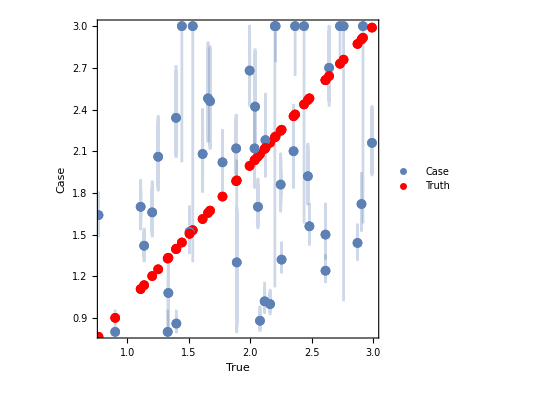

```mathematica
Show[Table[CICasePlot[testTreeList[[j]]],{j,1,maxn(*Length[testTreeList]*)}]]
```

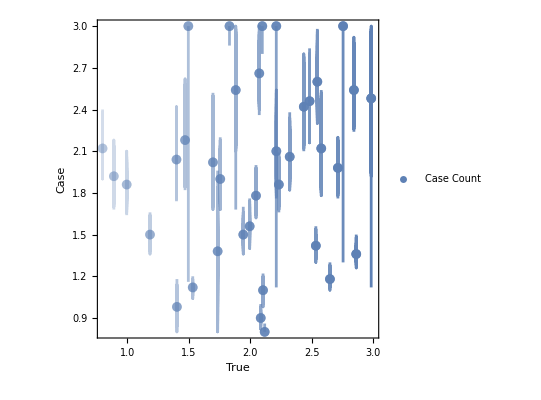

```mathematica
legCICase=PointLegend[{ColorData[97][1]},{"Case Count"}];

CICasePlot[intS_]:=Block[{βTrue},βTrue=β/. testParsSIR2[intS];
Show[(*Maximum Posterior Estimates*)ListPlot[{{{βTrue,ℒCMPE[intS]}}},PlotMarkers->{Graphics[{EdgeForm[],Disk[]}],Medium},PlotStyle->Directive[ColorData[97][1],Opacity[Abs[βTrue]/3]]],(*Credible Intervals*)ListLinePlot[{Map[{βTrue,#}&,ℒCCI[intS]]},AspectRatio->1,PlotStyle->{Directive[ColorData[97][1],Opacity[Abs[βTrue]/3]]}],AspectRatio->1,PlotRange->{{0.8,3},{0.8,3}},Epilog->Inset[legCICase,Scaled[{0.85,0.12}]],Frame->True,Axes->False,FrameLabel->{" True","  Case"},LabelStyle->Directive[Black,Medium]]]

Show[Table[CICasePlot[testTreeList[[j]]],{j,1,maxn}]]
```

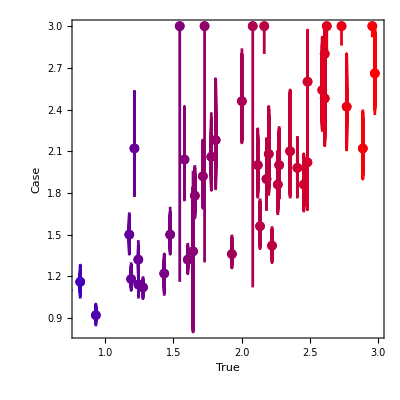

```mathematica
CICasePlot[intS_]:=Block[{βTrue},βTrue=β/. testParsSIR2[intS];
Show[(*Maximum Posterior Estimates*)ListPlot[{{{βTrue,ℒCMPE[intS]}}},PlotMarkers->{Graphics[{EdgeForm[],Disk[]}],Medium},PlotStyle->(Directive[Blend[{Blue,Red},Abs[βTrue]/3],Opacity[1]])],(*Credible Intervals*)ListLinePlot[{Map[{βTrue,#}&,ℒCCI[intS]]},AspectRatio->1,PlotStyle->(Directive[Blend[{Blue,Red},Abs[βTrue]/3],Opacity[1]])],AspectRatio->1,PlotRange->{{0.8,3},{0.8,3}},Frame->True,Axes->False,FrameLabel->{" True","  Case"},LabelStyle->Directive[Black,Medium]]]

Show[Table[CICasePlot[testTreeList[[j]]],{j,1,maxn}]]
```

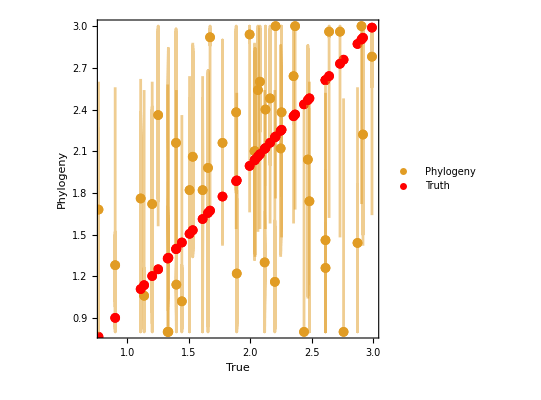

```mathematica
legCIPhylo=PointLegend[{col2,Red},{"Phylogeny","Truth"}];

CICasePlot[intS_]:=Block[{βTrue},βTrue=β/. testParsSIR2[intS];
Show[(*Maximum Posterior Estimates*)ListPlot[{{{βTrue,ℒPMPE[intS]}}},PlotMarkers->{Graphics[{EdgeForm[],Disk[]}],Medium},PlotStyle->Directive[col2]],(*Credible Intervals*)ListLinePlot[{Map[{βTrue,#}&,ℒPCI[intS]]},AspectRatio->1,PlotStyle->{Directive[col2,Opacity[0.5]]}],
ListPlot[{{{βTrue,βTrue}}},PlotMarkers->{Automatic, Medium},PlotStyle->{Red}],
AspectRatio->1,PlotRange->{{0.8,3},{0.8,3}},Epilog->Inset[legCIPhylo,Scaled[{0.12,0.92}]],Frame->True,Axes->False,FrameLabel->{" True","  Phylogeny"},LabelStyle->Directive[Black,Medium]]]

Show[Table[CICasePlot[testTreeList[[j]]],{j,1,maxn}]]
```

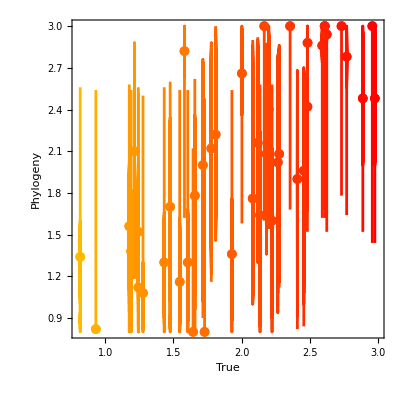

```mathematica
legCIPhyloPlot[intS_]:=Block[{βTrue},βTrue=β/. testParsSIR2[intS];
Show[(*Maximum Posterior Estimates*)ListPlot[{{{βTrue,ℒPMPE[intS]}}},PlotMarkers->{Graphics[{EdgeForm[],Disk[]}],Medium},PlotStyle->(Directive[Blend[{Yellow,Red},Abs[βTrue]/3],Opacity[1]])],(*Credible Intervals*)ListLinePlot[{Map[{βTrue,#}&,ℒPCI[intS]]},AspectRatio->1,PlotStyle->(Directive[Blend[{Yellow,Red},Abs[βTrue]/3],Opacity[1]])],AspectRatio->1,PlotRange->{{0.8,3},{0.8,3}},Frame->True,Axes->False,FrameLabel->{" True","  Phylogeny"},LabelStyle->Directive[Black,Medium]]]

Show[Table[legCIPhyloPlot[testTreeList[[j]]],{j,1,maxn}]]
```

```mathematica
cVec[testParsSIR2[observation],observation]
```

{4.5382,0.988089,0.49706,0.907479,0.863989,1.38816,2.90779,1.33811,1.38151,2.13816,1.44166,1.00966,5.01773,1.25519,5.59794,1.33389,2.26739,3.24009,1.55255,2.32015,2.17748,2.73997,4.04817,9.86595,2.02247,2.85477,3.3861,2.22713,6.90729,4.47561,2.31355,3.44849,3.57526,4.00444,4.80214,8.08115,3.27601,4.13604,2.99302,5.73107,3.8675,3.83542,4.58454,3.60536,4.09168,4.2194,7.05944,3.65717,9.29269,5.02026,5.74967,5.00825,6.78446,5.14068,8.62}

```mathematica
treeSize[intS_]:=Length[cVec[testParsSIR2[intS],intS]]
```

```mathematica
treeSize[observation]
```

55

```mathematica
testTreeList
```

{2,4,5,6,7,9,10,11,12,17,20,22,23,24,25,26,28,29,31,33,35,36,40,41,42,45,48,49,50,51,53,56,62,63,64,67,68,72,73,74,75,76,77,79,83,84,85,86,87,92,93,94,96,98,99,100}

8

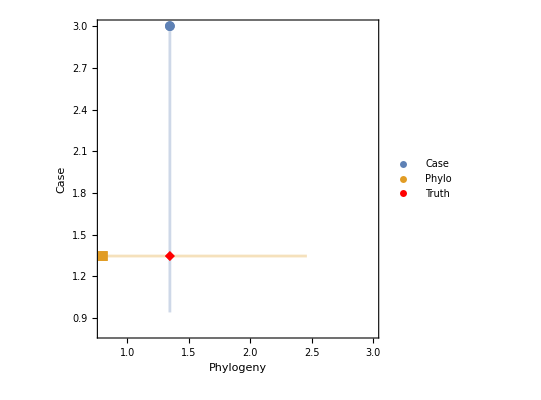

```mathematica
observation = 8
CICompPlot[observation]
```

```mathematica
cVec[testParsSIR2[observation],observation]
```

{0.183586}

```mathematica
treeSize[intS_]:=Length[cVec[testParsSIR2[intS],intS]]
```

```mathematica
treeSize[observation]
```

0

## Correlation

Calculating correlation of case counts posterior estimate

```mathematica
dataCMPE=Table[{β/. testParsSIR2[testTreeList[[j]]],ℒCMPE[testTreeList[[j]]]},{j,1,Length[testTreeList]}];
```

```mathematica
correlationCMPE=Correlation[dataCMPE[[All,1]],dataCMPE[[All,2]]]
```

0.234197

Calculating correlation of phylogeny posterior estimate

```mathematica
dataPMPE=Table[{ℒPMPE[testTreeList[[j]]],β/. testParsSIR2[testTreeList[[j]]]},{j,1,Length[testTreeList]}];
```

```mathematica
correlationPMPE=Correlation[dataPMPE[[All,1]],dataPMPE[[All,2]]]
```

0.377326

## Coverage

Calculating two lists that show 1 for hitting the truth and 0 for failing.

```mathematica
CoverageFunction[true_,{lower_,upper_}]:=If[lower<=true<=upper,1,0]
```

```mathematica
CaseCoverageList=Table[CoverageFunction[β/. testParsSIR2[testTreeList[[j]]],{Min[ℒCCI[testTreeList[[j]]]],Max[ℒCCI[testTreeList[[j]]]]}],{j,1,50}];
```

```mathematica
PhyloCoverageList=Table[CoverageFunction[β/. testParsSIR2[testTreeList[[j]]],{Min[ℒPCI[testTreeList[[j]]]],Max[ℒPCI[testTreeList[[j]]]]}],{j,1,50}];
```

```mathematica
CaseCoverageProbability=N[Total[CaseCoverageList]/maxn]
```

0.26

```mathematica
PhyloCoverageProbability=N[Total[PhyloCoverageList]/maxn]
```

0.76

## Precision

```mathematica
testTreeList
```

{1,2,3,7,10,11,12,15,16,20,21,22,23,24,30,31,32,33,38,39,40,41,42,43,44,45,47,51,53,54,55,57,58,60,61,65,66,69,70,72,74,75,76,80,81,82,85,86,89,90,92,94,96,97,99,100}

```mathematica
CIWidth[{lower_,upper_}]:=upper-lower
```

```mathematica
CaseWidths=Table[CIWidth[{Min[ℒCCI[testTreeList[[j]]]],Max[ℒCCI[testTreeList[[j]]]]}],{j,1,maxn}]
```

{0.8,0.84,1.32,0.26,0.5,1.88,0.46,0.74,0.14,0.06,0.56,0.2,0.16,0.26,0.52,0.76,0.16,0.18,0.24,0.36,0.2,0.42,1.84,0.5,0.68,0.34,0.64,0.22,0.68,0.22,0.68,0.08,0.24,0.64,0.44,0.5,0.38,1.16,0.68,0.3,0.2,0.5,1.88,0.24,1.7,0.78,0.38,0.7,0.52,0.3}

```mathematica
PhyloWidths=Table[CIWidth[{Min[ℒPCI[testTreeList[[j]]]],Max[ℒPCI[testTreeList[[j]]]]}],{j,1,maxn}]
```

{1.54,1.48,1.16,1.76,1.32,1.64,1.86,1.38,1.22,1.7,1.72,1.74,1.74,1.78,1.52,1.7,1.7,1.7,1.74,1.78,1.4,1.86,1.74,1.86,1.38,1.8,1.56,1.48,1.42,1.74,1.34,1.56,1.74,1.46,1.86,1.48,2.02,1.32,1.38,1.78,1.72,1.62,1.9,1.76,1.68,1.32,1.82,1.36,1.74,1.76}

Plotting normalized confidence interval (not normal yet)

```mathematica
widthCase[intS_]:=CIWidth[{Min[ℒCCI[intS]],Max[ℒCCI[intS]]}]
```

```mathematica
widthCasePlotAll:=Module[{widthCaseValues,betaValues},widthCaseValues=Table[widthCase[Part[testTreeList,i]],{i,1,Length[testTreeList]}];
betaValues=Table[β/. testParsSIR2[testTreeList[[i]]],{i,1,Length[testTreeList]}];
ListPlot[Transpose[{betaValues,widthCaseValues}],FrameLabel->{"β True","Case Counts CI's Width"},PlotLabel->"Case Counts CI's Width vs. β True",PlotRange->{All,{0,2.3}},PlotMarkers->{Automatic,Medium},PlotStyle->{Directive[col1]},Frame->True]]
```

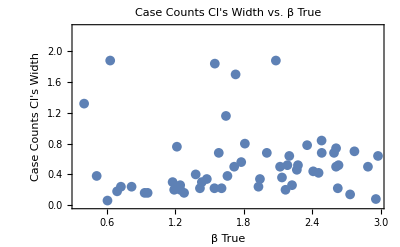

```mathematica
widthCasePlotAll
```

```mathematica
Export["/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report 2309/Figures/caseCI.png",%]
```

/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report 2309/Figures/caseCI.png

```mathematica
widthPhylo[intS_]:=CIWidth[{Min[ℒPCI[intS]],Max[ℒPCI[intS]]}]
```

```mathematica
widthPhyloPlotAll:=Module[{widthPhyloValues,betaValues},widthPhyloValues=Table[widthPhylo[Part[testTreeList,i]],{i,1,Length[testTreeList]}];
betaValues=Table[β/. testParsSIR2[testTreeList[[i]]],{i,1,Length[testTreeList]}];
ListPlot[Transpose[{betaValues,widthPhyloValues}],FrameLabel->{"β True","Phylogeny CI's Width"},PlotLabel->"Phylogeny CI's Width vs. β True",PlotRange->{All,{0,2.3}},PlotMarkers->{Automatic,Medium},PlotStyle->{Directive[col2]},Frame->True]]
```

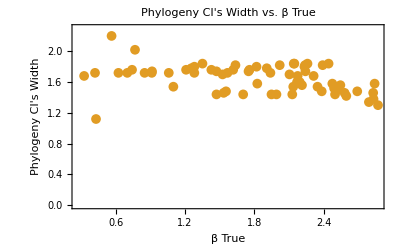

```mathematica
widthPhyloPlotAll
```

```mathematica
Export["/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report 2309/Figures/phyloCI.png",%]
```

/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report 2309/Figures/phyloCI.png

```mathematica
"/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report/Figures/phyloCI.png"
```

```mathematica
Mean[1/CaseWidths]
```

3.01458

```mathematica
Mean[1/PhyloWidths]
```

0.629139

```mathematica
PrecCase[ints_]:=1/CIWidth[{Min[ℒCCI[ints]],Max[ℒCCI[ints]]}]
```

```mathematica
PrecCase[3]
```

0.649351

```mathematica
PrecPhylo[ints_]:=1/CIWidth[{Min[ℒPCI[ints]],Max[ℒPCI[ints]]}]
```

```mathematica
PrecPhylo[3]
```

0.806452

Plot of precision based on beta true values

```mathematica
PrCompPlot[intS_] := Block[{βTrue},
  βTrue = β /. testParsSIR2[intS];
  Show[
   (*Maximum Posterior Estimates*)
   ListPlot[{{{βTrue, PrecCase[intS]}}, {{βTrue, 
       PrecPhylo[intS]}}}, PlotMarkers -> {Automatic, Medium}, 
    PlotStyle -> {Automatic, Automatic, Red}],
   PlotRange -> {{0, 4}, {0, 4}}, 
   Epilog -> Inset[leg, Scaled[{0.9, 0.75}]], Frame -> True, 
   Axes -> False, FrameLabel->{"β true","Precision"},
   LabelStyle -> Directive[Black, Medium]]]
```

```mathematica
Show[Table[PrCompPlot[testTreeList[[j]]],{j,1,maxn(*Length[testTreeList]*)}]]
```

-Graphics-

Plot of precision based on tree size

```mathematica
PrCompPlotTree[intS_] := Block[{TreeSize},
  TreeSize = treeSize[intS];
  Show[
   (*Maximum Posterior Estimates*)
   ListPlot[{{{TreeSize, PrecCase[intS]}}, {{TreeSize, 
       PrecPhylo[intS]}}}, PlotMarkers -> {Automatic, Medium}, 
    PlotStyle -> {Automatic, Automatic, Red}],  PlotRange -> {{0, 100}, {0, 4}}, 
   Epilog -> Inset[leg, Scaled[{0.9, 0.75}]], Frame -> True, 
   Axes -> False,  FrameLabel->{"Tree Size","Precision"},
   LabelStyle -> Directive[Black, Medium]]]
```

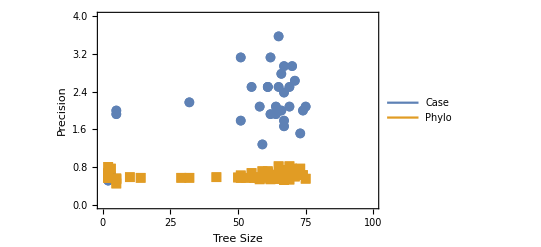

```mathematica
Show[Table[PrCompPlotTree[testTreeList[[j]]],{j,1,maxn(*Length[testTreeList]*)}]]
```

## Accuracy

```mathematica
AccuCaseSign[intS_]:=(β/. testParsSIR2[intS])-ℒCMPE[intS]
```

```mathematica
AccuPhyloSign[intS_]:=(β/. testParsSIR2[intS])-ℒPMPE[intS]
```

```mathematica
AccuCaseUnsign[intS_]:=Abs[(β/. testParsSIR2[intS])-ℒCMPE[intS]]
```

```mathematica
AccuPhyloUnsign[intS_]:=Abs[(β/. testParsSIR2[intS])-ℒPMPE[intS]]
```

```mathematica
RelErrorCase[intS_]:=Abs[((β/. testParsSIR2[intS])-ℒCMPE[intS])/(β/. testParsSIR2[intS])]
```

```mathematica
RelErrorPhylo[intS_]:=Abs[((β/. testParsSIR2[intS])-ℒPMPE[intS])/(β/. testParsSIR2[intS])]
```

```mathematica
(*Compute accuracies for each element of testTreeList*)
```

```mathematica
caseAccuracies=AccuCaseUnsign/@testTreeList;
```

```mathematica
phyloAccuracies=AccuPhyloUnsign/@testTreeList;
```

```mathematica
(*Combine the data*)
combinedData={caseAccuracies,phyloAccuracies};
```

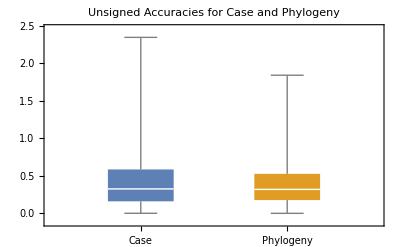

```mathematica
(*Make the box plot*)
BoxWhiskerChart[combinedData,ChartLabels->{"Case","Phylogeny"},ChartStyle->{Directive[col1],Directive[col2]},PlotLabel->"Unsigned Accuracies for Case and Phylogeny"]
```

Now, categorize iterations into low, medium and high beta

```mathematica
lowBetaList=Select[testTreeList,(β/. testParsSIR2[#])<1&];
mediumBetaList=Select[testTreeList,1<=(β/. testParsSIR2[#])<=2&];
highBetaList=Select[testTreeList,(β/. testParsSIR2[#])>2&];
```

```mathematica
lowBetaList
```

{3,11,20,23,33,38,66,80,96}

```mathematica
β/(γ+ψ)/. testParsSIR2[lowBetaList[[1]]]
```

0.666938

```mathematica
(β/(γ+ψ))/. testParsSIR2[#]&/@lowBetaList
```

{0.666938,1.048,1.0082,1.55162,1.1487,1.20443,0.850349,1.36044,1.59499}

```mathematica
mediumBetaList
```

{1,7,21,22,31,32,42,43,44,45,54,58,69,72,74,81,85,90,92,94,97,100}

```mathematica
β/. testParsSIR2[1]
```

1.80957

```mathematica
RelErrorCase[1]
```

0.204707

```mathematica
ℒCMPE[1]
```

2.18

```mathematica
(ℒCMPE[1]-β/. testParsSIR2[1])/β/. testParsSIR2[1]
```

0.204707

Compute unsinged accuracies for each category (low, medium, high) for both cases and phylogenies.

```mathematica
caseAccuraciesLow=AccuCaseUnsign/@lowBetaList;
phyloAccuraciesLow=AccuPhyloUnsign/@lowBetaList;

caseAccuraciesMedium=AccuCaseUnsign/@mediumBetaList;
phyloAccuraciesMedium=AccuPhyloUnsign/@mediumBetaList;

caseAccuraciesHigh=AccuCaseUnsign/@highBetaList;
phyloAccuraciesHigh=AccuPhyloUnsign/@highBetaList;
```

Make the box plot for each category.

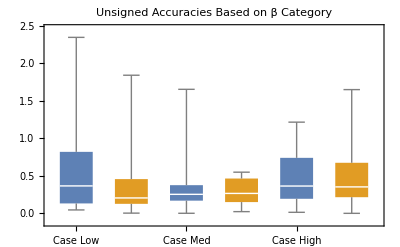

```mathematica
BoxWhiskerChart[{caseAccuraciesLow,phyloAccuraciesLow,caseAccuraciesMedium,phyloAccuraciesMedium,caseAccuraciesHigh,phyloAccuraciesHigh},ChartLabels->{"Case Low","Phylo Low","Case Med","Phylo Med","Case High","Phylo High"},ChartStyle->{Directive[col1],Directive[col2],Directive[col1],Directive[col2],Directive[col1],Directive[col2]},PlotLabel->"Unsigned Accuracies Based on β Category"]
```

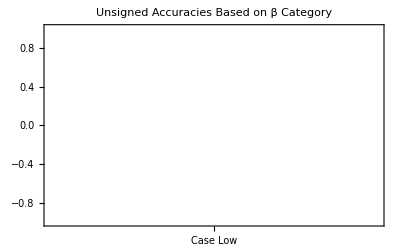

```mathematica
BoxWhiskerChart[{caseAccuraciesLow,caseAccuraciesMedium,caseAccuraciesHigh,phyloAccuraciesLow,phyloAccuraciesMedium,phyloAccuraciesHigh},ChartLabels->{"Case Low","Case Med","Case High","Phylo Low","Phylo Med","Phylo High"},ChartStyle->{Directive[col1],Directive[col1],Directive[col1],Directive[col2],Directive[col2],Directive[col2]},PlotLabel->"Unsigned Accuracies Based on β Category"]
```

Compute signed accuracies for each category (low, medium, high) for both cases and phylogenies.

```mathematica
caseAccuraciesLowSign=AccuCaseSign/@lowBetaList;
phyloAccuraciesLowSign=AccuPhyloSign/@lowBetaList;

caseAccuraciesMediumSign=AccuCaseSign/@mediumBetaList;
phyloAccuraciesMediumSign=AccuPhyloSign/@mediumBetaList;

caseAccuraciesHighSign=AccuCaseSign/@highBetaList;
phyloAccuraciesHighSign=AccuPhyloSign/@highBetaList;
```

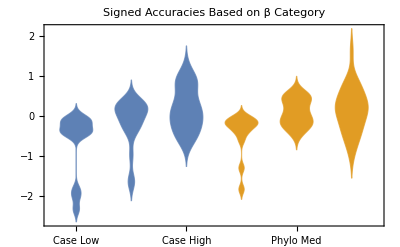

```mathematica
DistributionChart[{caseAccuraciesLowSign,caseAccuraciesMediumSign,caseAccuraciesHighSign,phyloAccuraciesLowSign,phyloAccuraciesMediumSign,phyloAccuraciesHighSign},ChartLabels->{"Case Low","Case Med","Case High","Phylo Low","Phylo Med","Phylo High"},ChartStyle->{Directive[col1],Directive[col1],Directive[col1],Directive[col2],Directive[col2],Directive[col2]},PlotLabel->"Signed Accuracies Based on β Category"]
```

Compute relative error for each beta category (low, medium, high) for both cases and phylogenies.

```mathematica
caseRelErrorLow=RelErrorCase/@lowBetaList;
phyloRelErrorLow=RelErrorPhylo/@lowBetaList;

caseRelErrorMedium=RelErrorCase/@mediumBetaList;
phyloRelErrorMedium=RelErrorPhylo/@mediumBetaList;

caseRelErrorHigh=RelErrorCase/@highBetaList;
phyloRelErrorHigh=RelErrorPhylo/@highBetaList;
```

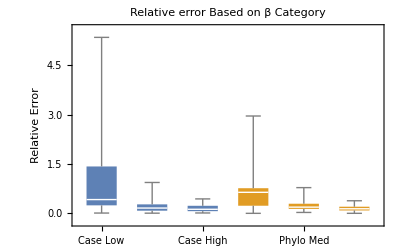

```mathematica
BoxWhiskerChart[{caseRelErrorLow,caseRelErrorMedium,caseRelErrorHigh,phyloRelErrorLow,phyloRelErrorMedium,phyloRelErrorHigh},ChartLabels->{"Case Low","Case Med","Case High","Phylo Low","Phylo Med","Phylo High"},ChartStyle->{Directive[col1],Directive[col1],Directive[col1],Directive[col2],Directive[col2],Directive[col2]},PlotLabel->"Relative error Based on β Category",FrameLabel->{{"Relative Error",None},{None,None}},LabelStyle->{Automatic,{Medium,10}}]
```

```mathematica
Export["/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report/Figures/relErrorBeta.png",%]
```

/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report/Figures/relErrorBeta.png

Plot based on tree size

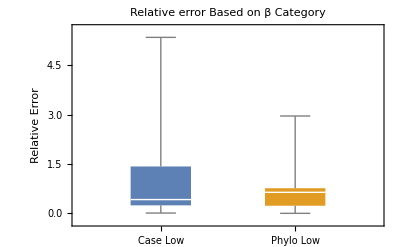

```mathematica
BoxWhiskerChart[{caseRelErrorLow,phyloRelErrorLow},ChartLabels->{"Case Low","Phylo Low"},ChartStyle->{Directive[col1],Directive[col2]},PlotLabel->"Relative error Based on β Category",FrameLabel->{{"Relative Error",None},{None,None}},LabelStyle->{Automatic,{Medium,10}}]
```

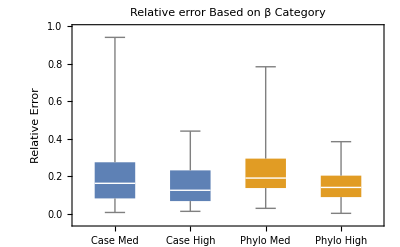

```mathematica
BoxWhiskerChart[{caseRelErrorMedium,caseRelErrorHigh,phyloRelErrorMedium,phyloRelErrorHigh},ChartLabels->{"Case Med","Case High","Phylo Med","Phylo High"},ChartStyle->{Directive[col1],Directive[col1],Directive[col2],Directive[col2]},PlotLabel->"Relative error Based on β Category",FrameLabel->{{"Relative Error",None},{None,None}},LabelStyle->{Automatic,{Medium,10}}]
```

```mathematica
smallTreeList=Select[testTreeList,treeSize[#]<20&];
mediumTreeList=Select[testTreeList,20<=treeSize[#]<=60&];
largeTreeList=Select[testTreeList,treeSize[#]>60&];
```

Compute unsinged accuracies for each category of tree sizes (small, medium, large) for both cases and phylogenies.

```mathematica
caseAccuraciesSmall=AccuCaseUnsign/@smallTreeList;
phyloAccuraciesSmall=AccuPhyloUnsign/@smallTreeList;

caseAccuraciesMediumTree=AccuCaseUnsign/@mediumTreeList;
phyloAccuraciesMediumTree=AccuPhyloUnsign/@mediumTreeList;

caseAccuraciesLarge=AccuCaseUnsign/@largeTreeList;
phyloAccuraciesLarge=AccuPhyloUnsign/@largeTreeList;
```

Make the box plot for each category .

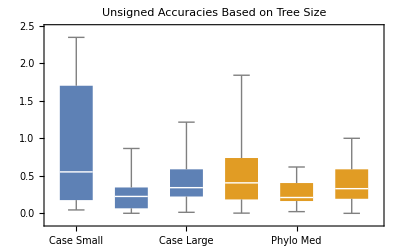

```mathematica
BoxWhiskerChart[{caseAccuraciesSmall,caseAccuraciesMediumTree,caseAccuraciesLarge,phyloAccuraciesSmall,phyloAccuraciesMediumTree,phyloAccuraciesLarge},ChartLabels->{"Case Small","Case Med","Case Large","Phylo Small","Phylo Med","Phylo Large"},ChartStyle->{Directive[col1],Directive[col1],Directive[col1],Directive[col2],Directive[col2],Directive[col2]},PlotLabel->"Unsigned Accuracies Based on Tree Size"]
```

Compute signed accuracies for each tree size category (small, medium, large) for both cases and phylogenies .

```mathematica
caseAccuraciesSmallSign=AccuCaseSign/@smallTreeList;
phyloAccuraciesSmallSign=AccuPhyloSign/@smallTreeList;

caseAccuraciesMediumTreeSign=AccuCaseSign/@mediumTreeList;
phyloAccuraciesMediumTreeSign=AccuPhyloSign/@mediumTreeList;

caseAccuraciesLargeSign=AccuCaseSign/@largeTreeList;
phyloAccuraciesLargeSign=AccuPhyloSign/@largeTreeList;
```

Distribution plot for tree size

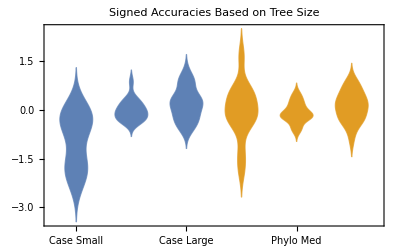

```mathematica
DistributionChart[{caseAccuraciesSmallSign,caseAccuraciesMediumTreeSign,caseAccuraciesLargeSign,phyloAccuraciesSmallSign,phyloAccuraciesMediumTreeSign,phyloAccuraciesLargeSign},ChartLabels->{"Case Small","Case Med","Case Large","Phylo Small","Phylo Med","Phylo Large"},ChartStyle->{Directive[col1],Directive[col1],Directive[col1],Directive[col2],Directive[col2],Directive[col2]},PlotLabel->"Signed Accuracies Based on Tree Size"]
```

Compute relative error for each tree size category (small, medium, large) for both cases and phylogenies .

```mathematica
caseRelErrorSmall=RelErrorCase/@smallTreeList;
phyloRelErrorSmall=RelErrorPhylo/@smallTreeList;

caseRelErrorMediumTree=RelErrorCase/@mediumTreeList;
phyloRelErrorMediumTree=RelErrorPhylo/@mediumTreeList;

caseRelErrorLarge=RelErrorCase/@largeTreeList;
phyloRelErrorLarge=RelErrorPhylo/@largeTreeList;
```

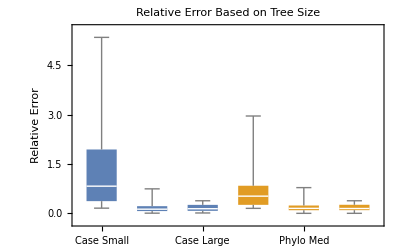

```mathematica
BoxWhiskerChart[{caseRelErrorSmall,caseRelErrorMediumTree,caseRelErrorLarge,phyloRelErrorSmall,phyloRelErrorMediumTree,phyloRelErrorLarge},ChartLabels->{"Case Small","Case Med","Case Large","Phylo Small","Phylo Med","Phylo Large"},ChartStyle->{Directive[col1],Directive[col1],Directive[col1],Directive[col2],Directive[col2],Directive[col2]},PlotLabel->"Relative Error Based on Tree Size",FrameLabel->{{"Relative Error",None},{None,None}},LabelStyle->{Automatic,{Medium,9}}]
```

```mathematica
Export["/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report/Figures/relErrorTree.png",%]
```

/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report/Figures/relErrorTree.png

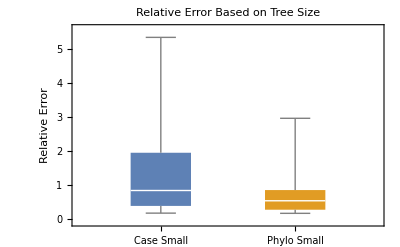

```mathematica
BoxWhiskerChart[{caseRelErrorSmall,phyloRelErrorSmall},ChartLabels->{"Case Small","Phylo Small"},ChartStyle->{Directive[col1],Directive[col2]},PlotLabel->"Relative Error Based on Tree Size",FrameLabel->{{"Relative Error",None},{None,None}},LabelStyle->{Automatic,{Medium,9}}]
```

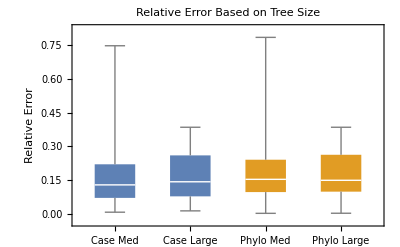

```mathematica
BoxWhiskerChart[{caseRelErrorMediumTree,caseRelErrorLarge,phyloRelErrorMediumTree,phyloRelErrorLarge},ChartLabels->{"Case Med","Case Large","Phylo Med","Phylo Large"},ChartStyle->{Directive[col1],Directive[col1],Directive[col2],Directive[col2]},PlotLabel->"Relative Error Based on Tree Size",FrameLabel->{{"Relative Error",None},{None,None}},LabelStyle->{Automatic,{Medium,9}}]
```

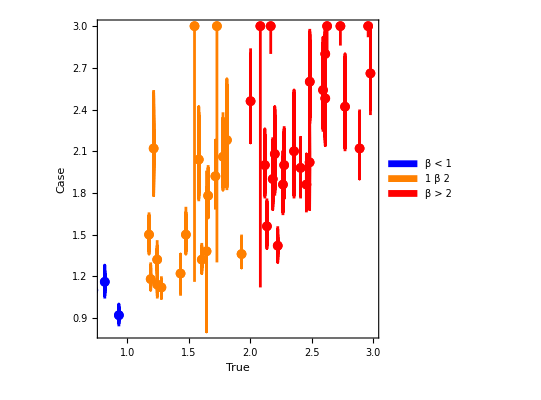

```mathematica
CICasePlotCat[intS_]:=Block[{βTrue,βRange},βTrue=β/. testParsSIR2[intS];
βRange=βTrue;
Module[{color},If[βRange<1,color=Blue,If[1<=βRange<=2,color=Orange,color=Red]];
Show[(*Maximum Posterior Estimates*)ListPlot[{{{βTrue,ℒCMPE[intS]}}},PlotMarkers->{Graphics[{EdgeForm[],Disk[]}],Medium},PlotStyle->(Directive[color,Opacity[1]])],(*Credible Intervals*)ListLinePlot[{Map[{βTrue,#}&,ℒCCI[intS]]},AspectRatio->1,PlotStyle->(Directive[color,Opacity[1]])],AspectRatio->1,PlotRange->{{0.8,3},{0.8,3}},Frame->True,Axes->False,FrameLabel->{" True","  Case"},LabelStyle->Directive[Black,Medium],Epilog->Inset[SwatchLegend[{Blue,Orange,Red},{"β < 1","1  β  2","β > 2"}],Scaled[{0.9,0.1}]]]]]

Show[Table[CICasePlotCat[testTreeList[[j]]],{j,1,maxn}]]
```

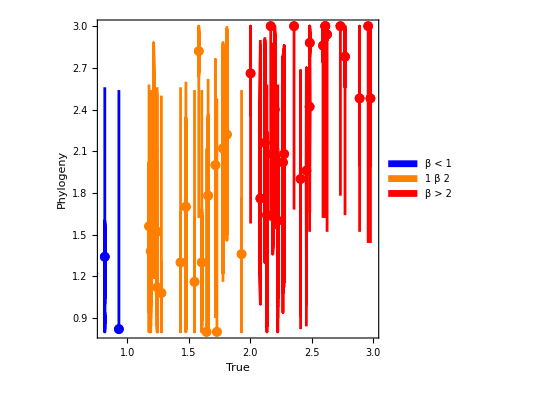

```mathematica
CIPhyloPlotCat[intS_]:=Block[{βTrue,βRange},βTrue=β/. testParsSIR2[intS];
βRange=βTrue;
Module[{color},If[βRange<1,color=Blue,If[1<=βRange<=2,color=Orange,color=Red]];
Show[(*Maximum Posterior Estimates*)ListPlot[{{{βTrue,ℒPMPE[intS]}}},PlotMarkers->{Graphics[{EdgeForm[],Disk[]}],Medium},PlotStyle->(Directive[color,Opacity[1]])],(*Credible Intervals*)ListLinePlot[{Map[{βTrue,#}&,ℒPCI[intS]]},AspectRatio->1,PlotStyle->(Directive[color,Opacity[1]])],AspectRatio->1,PlotRange->{{0.8,3},{0.8,3}},Frame->True,Axes->False,FrameLabel->{" True","  Phylogeny"},LabelStyle->Directive[Black,Medium],Epilog->Inset[SwatchLegend[{Blue,Orange,Red},{"β < 1","1  β  2","β > 2"}],Scaled[{0.9,0.1}]]]]]

Show[Table[CIPhyloPlotCat[testTreeList[[j]]],{j,1,maxn}]]
```

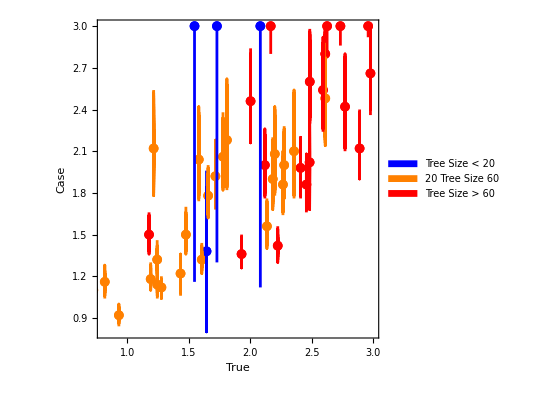

```mathematica
CICasePlotCatTree[intS_]:=Block[{βTrue,βRange,treeSizeCategory},βTrue=β/. testParsSIR2[intS];
βRange=βTrue;
treeSizeCategory=Which[treeSize[intS]<20,"Small",20<=treeSize[intS]<=60,"Medium",treeSize[intS]>60,"Large"];
Module[{color},Switch[treeSizeCategory,"Small",color=Blue,"Medium",color=Orange,"Large",color=Red];
Show[(*Maximum Posterior Estimates*)ListPlot[{{{βTrue,ℒCMPE[intS]}}},PlotMarkers->{Graphics[{EdgeForm[],Disk[]}],Medium},PlotStyle->(Directive[color,Opacity[1]])],(*Credible Intervals*)ListLinePlot[{Map[{βTrue,#}&,ℒCCI[intS]]},AspectRatio->1,PlotStyle->(Directive[color,Opacity[1]])],AspectRatio->1,PlotRange->{{0.8,3},{0.8,3}},Frame->True,Axes->False,FrameLabel->{" True","  Case"},LabelStyle->Directive[Black,Medium],Epilog->Inset[SwatchLegend[{Blue,Orange,Red},{"Tree Size < 20","20  Tree Size  60","Tree Size > 60"}],Scaled[{0.82,0.1}]]]]]

Show[Table[CICasePlotCatTree[testTreeList[[j]]],{j,1,maxn}]]
```

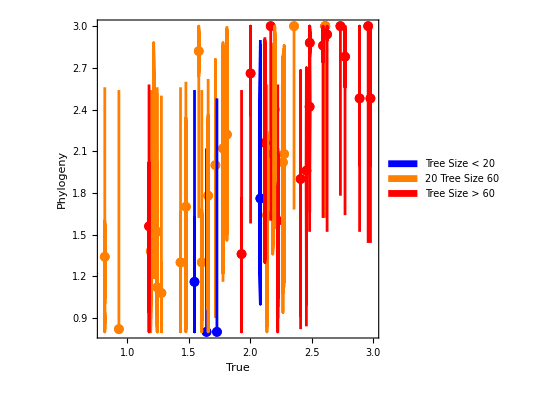

```mathematica
CIPhyloPlotCatTree[intS_]:=Block[{βTrue,βRange,treeSizeCategory},βTrue=β/. testParsSIR2[intS];
βRange=βTrue;
treeSizeCategory=Which[treeSize[intS]<20,"Small",20<=treeSize[intS]<=60,"Medium",treeSize[intS]>60,"Large"];
Module[{color},Switch[treeSizeCategory,"Small",color=Blue,"Medium",color=Orange,"Large",color=Red];
Show[(*Maximum Posterior Estimates*)ListPlot[{{{βTrue,ℒPMPE[intS]}}},PlotMarkers->{Graphics[{EdgeForm[],Disk[]}],Medium},PlotStyle->(Directive[color,Opacity[1]])],(*Credible Intervals*)ListLinePlot[{Map[{βTrue,#}&,ℒPCI[intS]]},AspectRatio->1,PlotStyle->(Directive[color,Opacity[1]])],AspectRatio->1,PlotRange->{{0.8,3},{0.8,3}},Frame->True,Axes->False,FrameLabel->{" True","  Phylogeny"},LabelStyle->Directive[Black,Medium],Epilog->Inset[SwatchLegend[{Blue,Orange,Red},{"Tree Size < 20","20  Tree Size  60","Tree Size > 60"}],Scaled[{0.82,0.1}]]]]]

Show[Table[CIPhyloPlotCatTree[testTreeList[[j]]],{j,1,maxn}]]
```